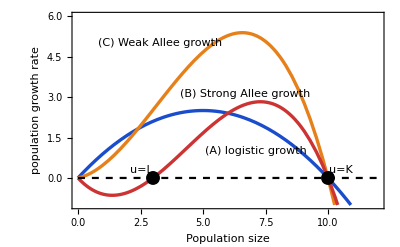

```mathematica
ρ=1;κ=10;τ=3;c=0.2;
p=Plot[{ρ*u*(1-u/κ),ρ*u*(1-u/κ)*(u/τ+c),ρ*u*(1-u/κ)*(u/τ-1),0},{u,0,κ+2},PlotStyle->{{RGBColor[0.1,0.3,0.8],Thickness[0.006]},{RGBColor[0.9,0.5,0.1],Thickness[0.006]},{RGBColor[0.8,0.2,0.2],Thickness[0.006]},{Black,Dashed,,Thickness[0.004]}},PlotRange->{{0,12},{-1,6}},Axes->False,Frame->True,FrameStyle->Directive[Black,Thickness[0.003]],FrameLabel->{"Population size","population growth rate"},Epilog->{Style[Text["(C) Weak Allee growth",{3.3,5}],FontSize->10,RGBColor[0.9,0.5,0.1]],Style[Text["(B) Strong Allee growth",{6.7,3.1}],FontSize->10, RGBColor[0.8,0.2,0.2]],Style[Text["(A) logistic growth",{7.13,1}],FontSize->10, RGBColor[0.1,0.3,0.8]],Style[Text["u=L",{2.55,0.3}],FontSize->12,Black,Background->None],Style[Text["u=K",{10.5,0.3}],FontSize->12,Bold,Black,Background->None]}];
q=Graphics[{Black,PointSize[0.025],Point[{10,0}]}];
q1=Graphics[{Black,PointSize[0.025],Point[{3,0}]}];
r=Show[p,q,q1]
```

```mathematica
Export[SystemDialogInput["FileSave","Allee.jpg"],r,ImageResolution->350,"CompressionLevel"->0]
```

C:\Users\SANTANA\Dropbox\SANTANA\P7_G function\Latex_manuscript\Allee.jpg